Consider a multichannel quantum system, modelled by a wavefunction:

Ψ(r,ω) = ∑_i (F_i(r) ϕ(ω))/r

where the sum is over the channels, F_i(r) is the “channel wavefunction” for each channel, i, and ϕ(ω) contains the (channel independent) dependence of Ψ on variables other than r.

We would like to model multichannel scattering using a potential that is piecewise constant.  Specifically, the potential will take the form:

V_((.08)_(i i))(r) = (E^th)_i              r > r_0
V_(i j)(r) = 0  for  i≠j   r > r_0

(V_(i j)(r))^†=V_(i j)(r) = constant   r < r_0
.08V_(i i)(r) = constant                  r < r_0

Thus, we have coupled square wells, with asymptotic energies in each channel of (E^th)_i.

This system can be solved exactly through the following method:

First, the solutions for each channel in the external region is simply a Bessel function (either an oscillating one, or a decaying one, depending on E-(E^th)_i).

In the interior region, we can find the solutions by diagonalizing V.  Since V is constant, there is a constant matrix U, such that:

Λ = UVU^T
U^T U = U U^T=1

with Λ diagonal.

We then have (with H in units of ℏ/(2m)):

(H - E)ψ = 0  →  -ψ’’ + (V - E)ψ = 0  →  U^T(-(U ψ)'' + (Λ - E)(U ψ))=0  →  -ϕ'' + (Λ - E)ϕ=0

where ϕ(r) = U ψ(r)  →  ψ(r) = U^T ϕ(r).  Now, ϕ can be solved for exactly, since Λ is diagonal.  If ϕ_α is a complete set of solutions (nicely chosen so that ϕ_i is zero in every channel except channel i), then the generic solution in the untransformed problem is: ψ_i(r) = ∑_α b_α (U^T)_(i α)ϕ_α(r), since any linear combination of the ϕ’s is another solution to the diagonalized problem.

Thus, if we let Φ_(i α)=(U^T)_(i α) ϕ_α, we can solve for the full wavefunction by matching linear combinations of the Φ’s onto the exterior solution and matching their derivatives:

(Φ_11 | ⋯ | Φ_(1N) | -g_1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
(∂Φ_11)/(∂r) | ⋯ | (∂Φ_(1N))/(∂r) | -(∂g_1)/(∂r) | 0 | 0 | 0 | 0 | 0 | 0 | 0
⋮ | ⋱ | ⋮ | 0 | ⋱ | 0 | 0 | 0 | 0 | 0 | 0
Φ_(N-N_o,1) | ⋯ | Φ_(N-N_o,N) | 0 | 0 | -g_(N-N_o) | 0 | 0 | 0 | 0 | 0
(∂Φ_(N-N_o,1))/(∂r) | ⋯ | (∂Φ_(N-N_o,N))/(∂r) | 0 | 0 | -(∂g_(N-N_o))/(∂r) | 0 | 0 | 0 | 0 | 0
Φ_(N-N_o+1,1) | ⋯ | Φ_(N-N_o+1,N) | 0 | 0 | 0 | -f_o | -g_o | 0 | 0 | 0
(∂Φ_(N-N_o+1,1))/(∂r) | ⋯ | (∂Φ_(N-N_o+1,N))/(∂r) | 0 | 0 | 0 | -(∂f_o)/(∂r) | -(∂g_o)/(∂r) | 0 | 0 | 0
⋮ | ⋱ | ⋮ | 0 | 0 | 0 | 0 | 0 | ⋱ | 0 | 0
Φ_(N,1) | ⋯ | Φ_(N,N) | 0 | 0 | 0 | 0 | 0 | 0 | -f_o | -g_o
(∂Φ_(N,1))/(∂r) | ⋯ | (∂Φ_(N,N))/(∂r) | 0 | 0 | 0 | 0 | 0 | 0 | -(∂f_o)/(∂r) | -(∂g_o)/(∂r)
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | ⋯ | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | ⋯ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | ⋱ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)(b_1
⋮
b_N
a_1
⋮
a_(N-N_o)
I_(1,1)
J_(1,1)
I_(1,2)
J_(1,2)
⋮
I_(1,N_o)
J_(1,N_o))=(0
0
⋮
0
0
0
0
1
0
0
⋮
0)

So, in words, we match each closed channel (channels 1 through N-N_o), onto the exponentially decaying Bessel function, g_i, whose channel dependence is simply in the differing threshold energies of the channels (affecting “how negative” the kinetic energy of a particle in that channel is in the r→∞ limit).

We also match the open channels onto their exterior solutions, but since there are two such solutions (called here f_o and g_o), we have two coefficients on the “RHS”, I and J, for each channel.  We need to impose a condition on these coefficients, since there are actually N_o linearly independent solutions for ψ (these can be thought of as corresponding to the N_o channels that the particle can approach from).  We thus impose that I_(i,j)=δ_(i,j), which should be thought of as N_o different conditions, labeled by i; each one corresponding to a different solution, ψ_i.   The general solution is given by linear combinations of the ψ_i’s.  However, all of the information about how particles scatter off of this potential is contained in the “K-matrix”, which is defined as:

K=J (I )^-1

It is thus the matrix which gives the proper J’s for a given set of I’s so that the linear combinations of f_o’s and g_o’s in each channel with these I’s and J’s as coefficients form a solution to the full Schrodinger Equation.  It is directly related to the S-matrix, which gives the transition amplitudes between incoming and outgoing states, and just like the S-matrix, scattering cross-sections can be obtained directly from the K-matrix.

For our problem, the K-matrix can be obtained directly by inverting the matrix on the left side of the above equation, and multiplying the following equation on the left by our inverted matrix:

(0 | 0 | 0 | ⋯ | 0
0 | 0 | 0 | ⋯ | 0
⋮ | ⋮ | ⋮ | ⋱ | ⋮
0 | 0 | 0 | ⋯ | 0
1 | 0 | 0 | ⋯ | 0
0 | 0 | 0 | ⋯ | 0
0 | 1 | 0 | ⋯ | 0
0 | 0 | 0 | ⋯ | 0
0 | 0 | 1 | ⋯ | 0
0 | 0 | 0 | ⋯ | 0
⋮ | ⋮ | ⋮ | ⋱ | ⋮
0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0)

where the top block of all 0’s is N-N_o by N-N_o and the bottom block is 2 N_o rows by N_o columns.  

The K matrix is then obtained by throwing away the top N-N_o by N-N_o block and then throwing out every other row, starting with the very first row.

```mathematica
f[L_,k_,r_]=√(π/2 k r)BesselJ[L+1/2,k r];
df[L_,k_,r_]=Simplify[D[√(π/2 k r)BesselJ[L+1/2,k r],r]];
g[L_,k_,r_]=√(π/2 k r)BesselY[L+1/2,k r];
dg[L_,k_,r_]=Simplify[D[√(π/2 k r)BesselY[L+1/2,k r],r]];
gb[L_,κ_,r_]=√(2/π κ r)BesselK[L+1/2,κ r] ⅇ^(κ Rshift)/.Rshift->0.9;
dgb[L_,κ_,r_]=Simplify[D[gb[L,κ,r],r]];
fb[L_,κ_,r_]=√(2/π κ r)BesselI[L+1/2,k r];
dfb[L_,κ_,r_]=Simplify[D[√(2/π κ r)BesselI[L+1/2,k r],r]];
```

```mathematica
Energy=9.07172;
numChan=3;
numOpen=2;
r0=1;
γ=0.01;
V=Table[0,{i,1,numChan},{j,1,numChan}];
VExt={10,0,0};
Do[V[[i,i]]=-20+5*i,{i,1,numChan}];
Do[V[[1,i]]=γ; V[[i,1]]=γ,{i,2,numChan}];
Λvals = Simplify[Eigenvalues[V]];
U=Transpose[Table[FullSimplify[Normalize[Eigenvectors[V][[n]]]],{n,1,numChan}]];
```

```mathematica
SetupPotentialCO[numChan_,numOpen_,r0_,γ_,D0_,ΔD_]:=Module[{i,j,U,Λvals,V},V=Table[0,{i,1,numChan},{j,1,numChan}];
Do[V[[i,i]]=-D0+ΔD*i,{i,1,numChan}];
Do[V[[1,i]]=γ; V[[i,1]]=γ,{i,2,numChan}];
Λvals = Simplify[Eigenvalues[V]];
U=Transpose[Table[FullSimplify[Normalize[Eigenvectors[V][[i]]]],{i,1,numChan}]];
{V,Λvals,U}]
```

```mathematica
MatrixForm[V]
N[Λvals]
```

(-15 | 0.01 | 0.01
0.01 | -10 | 0
0.01 | 0 | -5)

{-15.,-9.99998,-4.99999}

```mathematica
ϕ[r0_,E_]:=f[0,E^(1/2),r0];
dϕ[r0_,E_]:=df[0,E^(1/2),r0];
```

```mathematica
Φ=Table[U[[i,j]]*N[ϕ[r0,Energy-Λvals[[j]]]],{i,1,numChan},{j,1,numChan}];
dΦ=Table[U[[i,j]]*N[dϕ[r0,Energy-Λvals[[j]]]],{i,1,numChan},{j,1,numChan}];
```

```mathematica
AB=Table[0,{i,1,2*numChan+numOpen},{j,1,2*numChan+numOpen}];

Do[AB[[2*i-1,j]]=Φ[[i,j]]; AB[[2*i,j]]=dΦ[[i,j]],{i,1,numChan},{j,1,numChan}];

Do[AB[[2*i-1,i+numChan]]=-N[gb[0,(VExt[[i]]-Energy)^(1/2),r0]]; AB[[2*i,i+numChan]]=-N[dgb[0,(VExt[[i]]-Energy)^(1/2),r0]],{i,1,numChan-numOpen}];

Do[AB[[2*i-1+2*(numChan-numOpen),2*i-1+2*numChan-numOpen]]=-N[f[0,(Energy-VExt[[i+numChan-numOpen]])^(1/2),r0]];
AB[[2*i-1+2*(numChan-numOpen),2*i+2*numChan-numOpen]]=-N[g[0,(Energy-VExt[[i+numChan-numOpen]])^(1/2),r0]];
AB[[2*i+2*(numChan-numOpen),2*i-1+2*numChan-numOpen]]=-N[df[0,(Energy-VExt[[i+numChan-numOpen]])^(1/2),r0]];
AB[[2*i+2*(numChan-numOpen),2*i+2*numChan-numOpen]]=-N[dg[0,(Energy-VExt[[i+numChan-numOpen]])^(1/2),r0]];, {i,1,numOpen}];

Do[AB[[i+2*numChan,2*i-1+2*numChan-numOpen]]=1,{i,1,numOpen}];
```

```mathematica
MatrixForm[AB]
```

(0.981256 | 0.00188195 | -0.000572569 | -0.908149 | 0 | 0 | 0 | 0
-0.945417 | 0.0029561 | -0.00307547 | 0.874977 | 0 | 0 | 0 | 0
-0.0019625 | 0.940981 | -1.14514×10^-6 | 0 | -0.1293 | -0.991606 | 0 | 0
0.00189082 | 1.47806 | -6.15093×10^-6 | 0 | 2.98665 | -0.389443 | 0 | 0
-0.000981253 | -3.76391×10^-6 | -0.572568 | 0 | 0 | 0 | -0.1293 | -0.991606
0.000945414 | -5.91223×10^-6 | -3.07547 | 0 | 0 | 0 | 2.98665 | -0.389443
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0)

```mathematica
b=Table[0,{i,1,numOpen},{j,1,2*numChan+numOpen}];
Do[b[[i,i+2*numChan]]=1,{i,1,numOpen}];
```

```mathematica
sols=Table[0,{i,1,numOpen}];
Do[sols[[i]]=LinearSolve[AB,b[[i]]],{i,1,numOpen}];
```

```mathematica
sols
```

{{-794.546,-0.832371,-0.370929,-858.51,1.,0.652226,0.,1.00043},{-234.976,0.564195,0.955842,-253.892,0.,1.00043,1.,-0.449791}}

```mathematica
K=Table[sols[[i,2*numChan-numOpen+2*j]],{i,1,numOpen},{j,1,numOpen}];
MatrixForm[K]
```

(0.652226 | 1.00043
1.00043 | -0.449791)

```mathematica
δvals =ArcTan[Eigenvalues[K]]
```

{0.893454,-0.805446}

```mathematica
S=(IdentityMatrix[numOpen]+ⅈ*K).Inverse[IdentityMatrix[numOpen]-ⅈ*K];
MatrixForm[S]
Abs[S[[2,1]]]^2
```

(-0.169315+0.465402 ⅈ | -0.0763591+0.865391 ⅈ
-0.0763591+0.865391 ⅈ | -0.0852024-0.48786 ⅈ)

0.754733

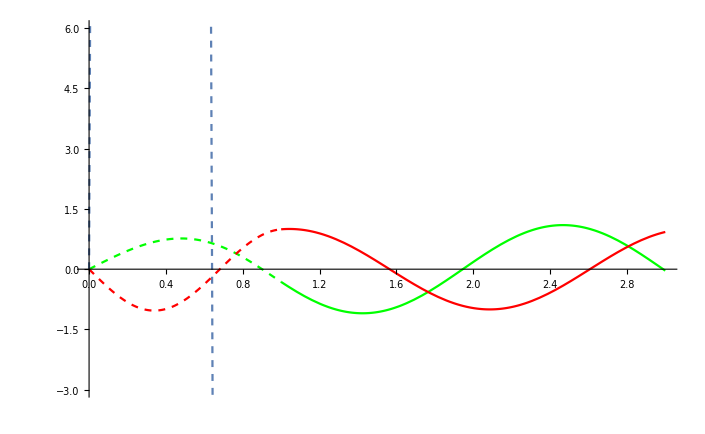

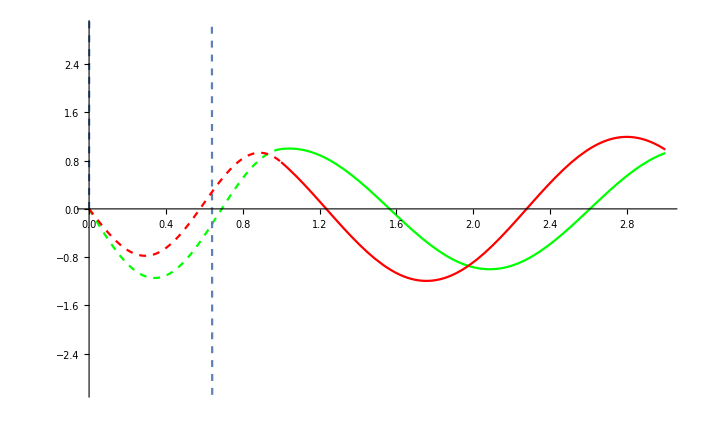

```mathematica
range = 3;
Show[Plot[U[[3,1]]*sols[[2,1]]*f[0,(Energy-Λvals[[1]])^(1/2),x]+U[[3,2]]*sols[[2,2]]*f[0,(Energy-Λvals[[2]])^(1/2),x]+U[[3,3]]*sols[[2,3]]*f[0,(Energy-Λvals[[3]])^(1/2),x],{x,0,r0},PlotStyle->{Green,Dashed},PlotRange->{{0,range*r0},{-3,6}}],Plot[sols[[2,numChan+4]]*f[0,(Energy+VExt[[3]])^(1/2),x]+sols[[2,numChan+5]]*g[0,(Energy+VExt[[3]])^(1/2),x],{x,r0,range*r0},PlotStyle->Green],Plot[U[[1,1]]*sols[[2,1]]*f[0,(Energy-Λvals[[1]])^(1/2),x]+U[[1,2]]*sols[[2,2]]*f[0,(Energy-Λvals[[2]])^(1/2),x]+U[[1,3]]*sols[[2,3]]*f[0,(Energy-Λvals[[3]])^(1/2),x],{x,0,r0},PlotStyle->Dashed],Plot[sols[[2,numChan+1]]*gb[0,(VExt[[1]]-Energy)^(1/2),x],{x,r0,range*r0}],Plot[U[[2,1]]*sols[[2,1]]*f[0,(Energy-Λvals[[1]])^(1/2),x]+U[[2,2]]*sols[[2,2]]*f[0,(Energy-Λvals[[2]])^(1/2),x]+U[[2,3]]*sols[[2,3]]*f[0,(Energy-Λvals[[3]])^(1/2),x],{x,0,r0},PlotStyle->{Red,Dashed}],Plot[sols[[2,numChan+2]]*f[0,(Energy+VExt[[2]])^(1/2),x]+sols[[2,numChan+3]]*g[0,(Energy+VExt[[2]])^(1/2),x],{x,r0,range*r0},PlotStyle->Red]]

Show[Plot[U[[3,1]]*sols[[1,1]]*f[0,(Energy-Λvals[[1]])^(1/2),x]+U[[3,2]]*sols[[1,2]]*f[0,(Energy-Λvals[[2]])^(1/2),x]+U[[3,3]]*sols[[1,3]]*f[0,(Energy-Λvals[[3]])^(1/2),x],{x,0,r0},PlotStyle->{Green,Dashed},PlotRange->{{0,range*r0},{-3,3}}],Plot[sols[[1,numChan+4]]*f[0,(Energy+VExt[[3]])^(1/2),x]+sols[[1,numChan+5]]*g[0,(Energy+VExt[[3]])^(1/2),x],{x,r0,range*r0},PlotStyle->Green],Plot[U[[1,1]]*sols[[1,1]]*f[0,(Energy-Λvals[[1]])^(1/2),x]+U[[1,2]]*sols[[1,2]]*f[0,(Energy-Λvals[[2]])^(1/2),x]+U[[1,3]]*sols[[1,3]]*f[0,(Energy-Λvals[[3]])^(1/2),x],{x,0,r0},PlotStyle->Dashed],Plot[sols[[1,numChan+1]]*gb[0,(VExt[[1]]-Energy)^(1/2),x],{x,r0,range*r0}],Plot[U[[2,1]]*sols[[1,1]]*f[0,(Energy-Λvals[[1]])^(1/2),x]+U[[2,2]]*sols[[1,2]]*f[0,(Energy-Λvals[[2]])^(1/2),x]+U[[2,3]]*sols[[1,3]]*f[0,(Energy-Λvals[[3]])^(1/2),x],{x,0,r0},PlotStyle->{Red,Dashed}],Plot[sols[[1,numChan+2]]*f[0,(Energy+VExt[[2]])^(1/2),x]+sols[[1,numChan+3]]*g[0,(Energy+VExt[[2]])^(1/2),x],{x,r0,range*r0},PlotStyle->Red]]
```

```mathematica
FindRoot[√(v0+ϵ) Cos[√(v0+ϵ)]+√-ϵ Sin[√(v0+ϵ)]/.v0->25,{ϵ,0}]
```

{ϵ→-0.928268+1.74289×10^-17 ⅈ}

```mathematica
10-0.928268
```

9.07173

```mathematica
SetupPotentialCO[numChan_,numOpen_,r0_,γ_,D0_,ΔD_]:=Module[{i,j,U,Λvals,V},V=Table[0,{i,1,numChan},{j,1,numChan}];
Do[V[[i,i]]=-D0+ΔD*i,{i,1,numChan}];
Do[V[[1,i]]=γ; V[[i,1]]=γ,{i,2,numChan}];
Λvals = Simplify[Eigenvalues[V]];
U=Transpose[Table[FullSimplify[Normalize[Eigenvectors[V][[i]]]],{i,1,numChan}]];
{V,Λvals,U}]
```

```mathematica
SetupΦ[numChan_,r0_,Λvals_,U_,Energy_]:=Module[{Φ,dΦ,i,j},Φ=Table[U[[i,j]]*N[ϕ[r0,Energy-Λvals[[j]]]],{i,1,numChan},{j,1,numChan}];
dΦ=Table[U[[i,j]]*N[dϕ[r0,Energy-Λvals[[j]]]],{i,1,numChan},{j,1,numChan}];
{Φ,dΦ}]
```

```mathematica
SetupABMat[numChan_,numOpen_,VExt_,Φ_,dΦ_,r0_,Energy_]:=Module[{i,j,AB,b},AB=Table[0,{i,1,2*numChan+numOpen},{j,1,2*numChan+numOpen}];

Do[AB[[2*i-1,j]]=Φ[[i,j]]; AB[[2*i,j]]=dΦ[[i,j]],{i,1,numChan},{j,1,numChan}];

Do[AB[[2*i-1,i+numChan]]=-N[gb[0,(VExt[[i]]-Energy)^(1/2),r0]]; AB[[2*i,i+numChan]]=-N[dgb[0,(VExt[[i]]-Energy)^(1/2),r0]],{i,1,numChan-numOpen}];

Do[AB[[2*i-1+2*(numChan-numOpen),2*i-1+2*numChan-numOpen]]=-N[f[0,(Energy-VExt[[i+numChan-numOpen]])^(1/2),r0]];
AB[[2*i-1+2*(numChan-numOpen),2*i+2*numChan-numOpen]]=-N[g[0,(Energy-VExt[[i+numChan-numOpen]])^(1/2),r0]];
AB[[2*i+2*(numChan-numOpen),2*i-1+2*numChan-numOpen]]=-N[df[0,(Energy-VExt[[i+numChan-numOpen]])^(1/2),r0]];
AB[[2*i+2*(numChan-numOpen),2*i+2*numChan-numOpen]]=-N[dg[0,(Energy-VExt[[i+numChan-numOpen]])^(1/2),r0]];, {i,1,numOpen}];

Do[AB[[i+2*numChan,2*i-1+2*numChan-numOpen]]=1,{i,1,numOpen}];

b=Table[0,{i,1,numOpen},{j,1,2*numChan+numOpen}];
Do[b[[i,i+2*numChan]]=1,{i,1,numOpen}];

{AB,b}]
```

```mathematica
FindKMat[numChan_,numOpen_,AB_,b_]:=Module[{i,j,sols,K},sols=Table[0,{i,1,numOpen}];
Do[sols[[i]]=LinearSolve[AB,b[[i]]],{i,1,numOpen}];
K=Table[sols[[i,2*numChan-numOpen+2*j]],{i,1,numOpen},{j,1,numOpen}];
{K,sols}]
```

```mathematica
FindKMatTotal[numChan_,numOpen_,r0_,Λvals_,U_,VExt_,Energy_]:=Module[{i,j,X,Y,Z,S},X=SetupΦ[numChan,r0,Λvals,U,Energy];
Y=SetupABMat[numChan,numOpen,VExt,X[[1]],X[[2]],r0,Energy];
Z=FindKMat[numChan,numOpen,Y[[1]],Y[[2]]];
S=(IdentityMatrix[numOpen]+ⅈ*Z[[1]]).Inverse[IdentityMatrix[numOpen]-ⅈ*Z[[1]]];
Append[Z,S]]
```

```mathematica
r0=1;
numChan=3;
numOpen=2;
D0=20;
ΔD=5;
γ=0.01;
X=SetupPotentialCO[numChan,numOpen,r0,γ,D0,ΔD];
VExt={10,0,0};
Z=FindKMatTotal[numChan,numOpen,r0,X[[2]],X[[3]],VExt,9.05];
K=Z[[1]];
EList=Table[i,{i,9.0716,9.0719,0.0000005}];
SList=Table[{EList[[i]],Abs[FindKMatTotal[numChan,numOpen,r0,X[[2]],X[[3]],VExt,EList[[i]]][[3]][[2,1]]]^2},{i,1,Length[EList]}];
```

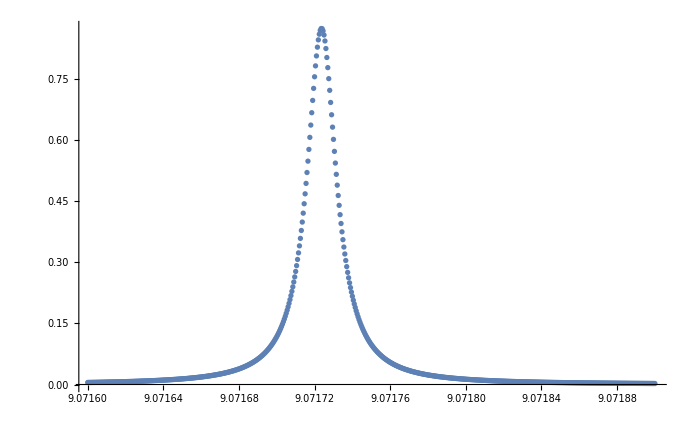

```mathematica
ListPlot[SList,PlotRange->All]
```

```mathematica
MatrixForm[Z[[1]]]
```

(-3.01521 | -0.0836461
-0.0836461 | -0.771576)